# Ei NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## Definitions and derivations

```mathematica
Ei`D[u_,α_]:=Gamma[0,(-1+1/u^2)/α^2]/(π u^4 α^2)HeavisideTheta[u]
```

```mathematica
Ei`Λ[u_,α_]:=(2 ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) α (-α^2+u^2 (-1+α^2))+√π u (3 α^2+u^2 (2-3 α^2)) Erfc[u/(√(1-u^2) α)])/(6 √π u (-1+u^2) α^2)
```

```mathematica
Ei`σ[u_,α_]:=1/(6 √π (-1+u^2) α^2)(α (3 √π u (-1+u^2) α+2 ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) (-α^2+u^2 (-1+α^2)))+3 √π u (-α^2+u^2 (-2+α^2)) Erf[u/(√(1-u^2) α)]+2 √π u^2 Abs[u] (1+2 Erf[(u^2 √(1-u^2))/(α Abs[u]-u^2 α Abs[u])]))
```

```mathematica
Ei`G1[u_,a_]:=1/(1+Ei`Λ[u,a])
```

```mathematica
FullSimplify[Ei`Λ[u,u/(√(1-u^2) x)],Assumptions->0<u<1&&x>0]
```

(ⅇ^(-x^2) (1+x^2))/(3 √π x)-1/6 (3+2 x^2) Erfc[x]

### derivation

```mathematica
Beckmann`D[u_,α_]:=(ⅇ^(-(-1+1/u^2)/α^2))/(α^2 π u^4)HeavisideTheta[u]
```

```mathematica
Integrate[Beckmann`D[u,α √m],{m,0,1},Assumptions->0<u<1&&α>0]
```

Gamma[0,(-1+1/u^2)/α^2]/(π u^4 α^2)

```mathematica
Integrate[Beckmann`σ[u,α √m],{m,0,1},Assumptions->-1<u<1&&α>0]
```

1/(6 √π (-1+u^2) α^2)(α (3 √π u (-1+u^2) α+2 ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) (-α^2+u^2 (-1+α^2)))+3 √π u (-α^2+u^2 (-2+α^2)) Erf[u/(√(1-u^2) α)]+2 √π u^2 Abs[u] (1+2 Erf[(u^2 √(1-u^2))/(α Abs[u]-u^2 α Abs[u])]))

```mathematica
Integrate[Beckmann`Λ[u,α √m],{m,0,1},Assumptions->0<u<1&&α>0]
```

(2 ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) α (-α^2+u^2 (-1+α^2))+√π u (3 α^2+u^2 (2-3 α^2)) Erfc[u/(√(1-u^2) α)])/(6 √π u (-1+u^2) α^2)

### shape invariant f(x)

```mathematica
FullSimplify[Ei`D[u,α] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0&&x>0&&α>0]
```

Gamma[0,x^2]/π

### height field normalization

```mathematica
Integrate[2Pi u Ei`D[u,α],{u,0,1},Assumptions->0<α<1]
```

1

### distribution of slopes

```mathematica
FullSimplify[Ei`D[1/(√(p^2+q^2+1)),α](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

Gamma[0,(p^2+q^2)/α^2]/(π α^2)

```mathematica
Ei`P22[p_,q_,α_]:=Gamma[0,(p^2+q^2)/α^2]/(π α^2)
```

```mathematica
Integrate[Ei`P22[p,q,α],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1]
```

1

### compare σ to delta integral:

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

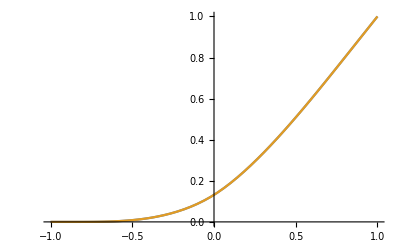

```mathematica
With[{α=.7},
Plot[{
Quiet[NIntegrate[Ei`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
Quiet[Ei`σ[u,α]]
},{u,-1,1}]
]
```